```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LC EOP\\EOP.xlsx"]
```

{{{0.,100.},{0.5,100.},{0.8,99.9333},{1.,98.9},{1.1,94.2333},{1.15,89.4667},{1.2,83.2667},{1.3,67.8667},{1.4,50.6333},{1.5,34.9333},{1.6,22.7333},{1.7,14.5333},{2.,4.9},{3.,4.7},{4.,4.4},{5.,4.},{6.,3.7}}}

```mathematica
data={{0.,100.},{0.5,100.},{0.8,99.93333333333334},{1.,98.90000000000002},{1.1,94.23333333333333},{1.15,89.46666666666665},{1.2,83.26666666666667},{1.3,67.86666666666666},{1.4,50.633333333333326},{1.5,34.93333333333334},{1.6,22.73333333333333},{1.7,14.533333333333333},{2.,4.9},{3.,4.7},{4.,4.4},{5.,4.},{6.,3.7000000000000006}}
```

{{0.,100.},{0.5,100.},{0.8,99.9333},{1.,98.9},{1.1,94.2333},{1.15,89.4667},{1.2,83.2667},{1.3,67.8667},{1.4,50.6333},{1.5,34.9333},{1.6,22.7333},{1.7,14.5333},{2.,4.9},{3.,4.7},{4.,4.4},{5.,4.},{6.,3.7}}

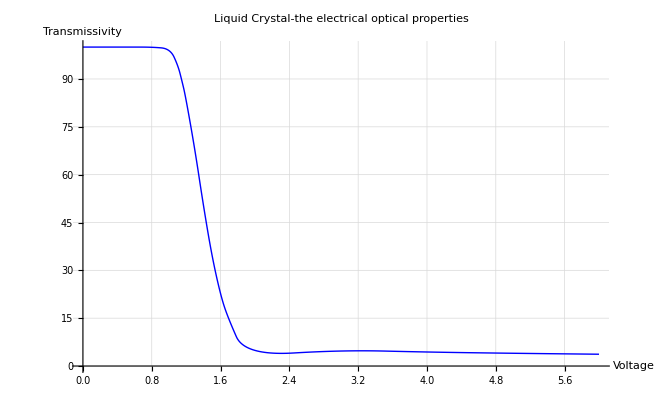

```mathematica
gra=ListLinePlot[data,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"Voltage","Transmissivity"},PlotLabel->"Liquid Crystal-the electrical optical properties",GridLines->Automatic]
```

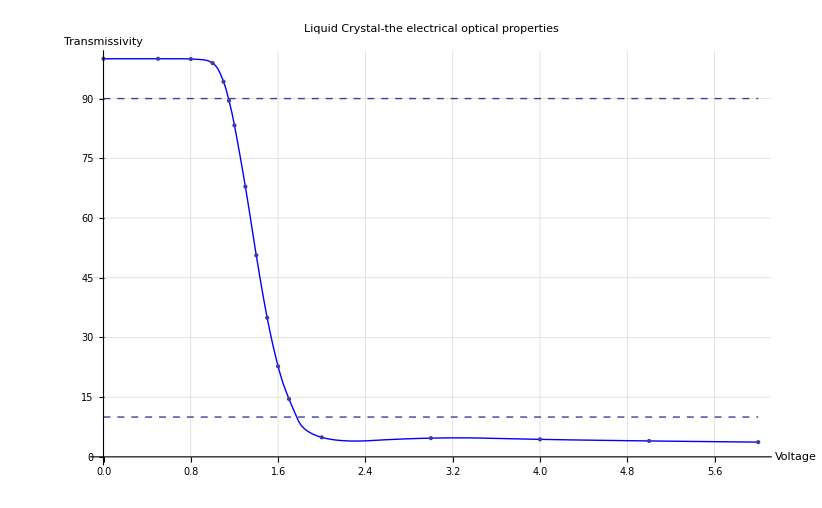

```mathematica
Show[gra,ListPlot[data],Plot[y=90,{x,0,6},PlotStyle->Dashed],Plot[y=10,{x,0,6},PlotStyle->Dashed]]
```